```mathematica
ClearAll["Global`*"](*To clear your variables before a fresh, full run of the notebook*)
ClearSystemCache[]
```

# COFLASY-M: COsmological evolution of FLAvour ASYmmetries - Mathematica

by Valerie Domcke (valerie.domcke@cern.ch), Miguel Escudero (miguel.escudero@cern.ch), Mario Fernandez Navarro (Mario.FernandezNavarro@glasgow.ac.uk), Stefan Sandner (stefan.sandner@lanl.gov)

If you use this code for scientific publications, please cite the paper:

“Lepton Flavour Asymmetries: from the early Universe to BBN.”  Valerie Domcke, Miguel Escudero, Mario Fernandez Navarro and Stefan Sandner
[arXiv:2502.14960] (https://arxiv.org/abs/2502.14960), [INSPIRE] (https://inspirehep.net/literature/2893306).

Last major update: 24-02-2025
v1.0

### Basic instructions

The code works as follows:

	1) Evaluate the “Basic module” section.
	2) The “Examples” section serves as a tutorial to use the code and generates some of the plots in [2502.XXXXXX]. Evaluating the full section may take around 15 min, some examples take only a few seconds while others    	take several minutes.

### Basic module

```mathematica
(* Load the basic module which contains all equations and functions to solve the system, takes around 10 seconds *)
SetDirectory[NotebookDirectory[]];
Get["BasicModule.m"]
```

### Examples

#### Benchmarks of the paper with FD collisions

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: 0.000213501

Thermodynamics are output to: output/output.dat

Total execution time: 2.904 s

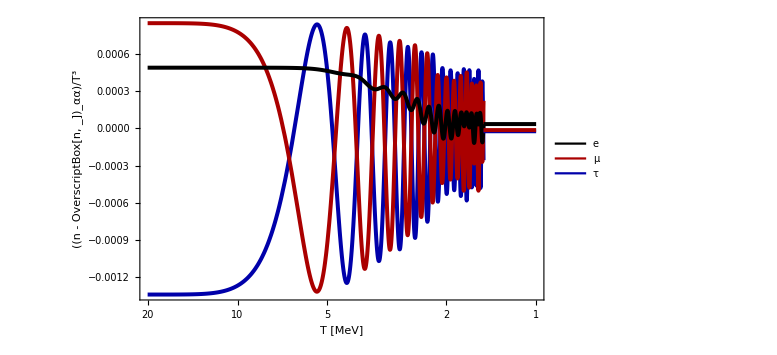

```mathematica
(*We provide initial conditions over (A,ϕ)*)
Aval=0.01;
ϕval=π/3;
(*We translate from (A,ϕ) to (ξe,ξμ,ξτ), alternatively the user may provide conditions over (ξe,ξμ,ξτ) directly*)
ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];

(*This is the minimum input required to run the solving functions, with all the optional arguments using default values*)
(*We run the system with FD collisions*)
Fig5aFD=solveFD[ξeini,ξμini,ξτini]
```

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: -0.0250915

Thermodynamics are output to: output/Fig5b.dat

Total execution time: 1.195 min

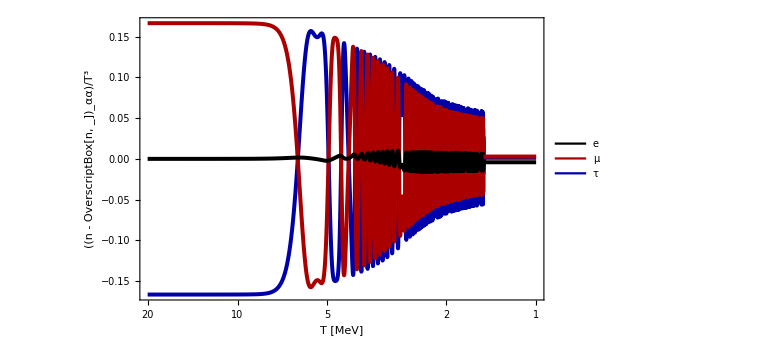

```mathematica
(*Alternatively, the user can define all the optional arguments to be used by the solving functions*)

(*We provide initial conditions over (A,ϕ)*)
Aval=√2;
ϕval=π/2;
ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];
(*Name for the .dat file containing the output*)
outputFilename="Fig5b";
(*We provide initial temperature (Tini), temperature at which oscillation average is taken (Tave), and we extend asymptotically the result at Tave until a final temperature (Tfinal)*)
(*Note we must provide Tini < Tave <= Tfinal for consistency*)
Tini=20MeV;
Tave=1.5MeV;
Tfinal=1MeV;
(*We provide accuracy and precision settings for NDSolve*)
accval=8;
precval=8;
(*The solving method used by NDSolve may also be specified*)
method="BDF";
(*Adiabatic=False runs the full system, while Adiabatic=True runs the system in the adiabatic approximationw where Vs=0*)
adiabatic=False;
(*Execution time in seconds after which the solver switches to the adiabatic approximation, useful for numerically challenging benchmarks*)
timeoutAdiabatic=300; 

Fig5bFD=solveFD[ξeini,ξμini,ξτini,outputFilename,Tini,Tave,Tfinal,accval,precval,method,adiabatic,timeoutAdiabatic]
```

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: 0.233341

Thermodynamics are output to: output/output.dat

Total execution time: 2.144 min

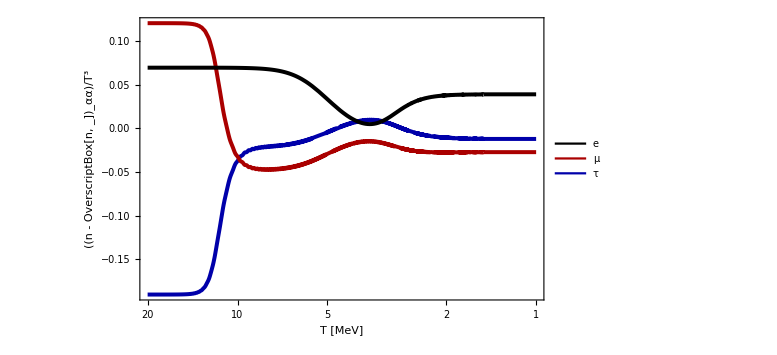

```mathematica
Aval=√2;
ϕval=π/3;

ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];

Fig3aFD=solveFD[ξeini,ξμini,ξτini]
```

Starting evolution of the full system

Timeout of 180s reached at T= 1.95249 MeV → Switching to adiabatic V_s=0

System evolved until T_ave=1.5 MeV

Final ξe: 0.0053012

Thermodynamics are output to: output/Fig3b.dat

Total execution time: 3.719 min

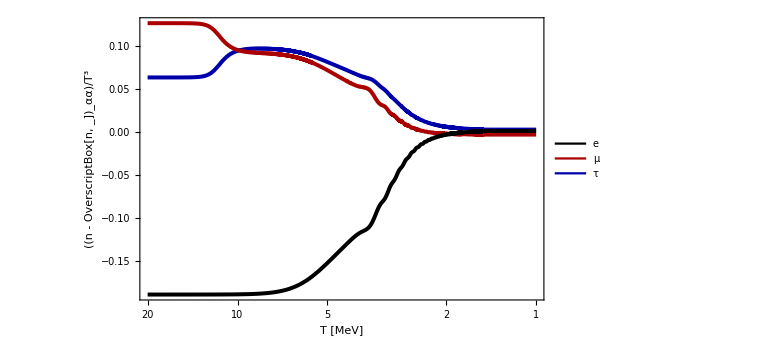

```mathematica
(*This benchmark is more numerically challenging and the solver gets stuck around T=2MeV, but fortunately the timeout switches to adiabatic and allows to reach Tave=1.5MeV*)

Aval=√2;
ϕval=ArcTan[-3,2];

ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];
Tini=20MeV;
Tave=1.5MeV;
Tfinal=1MeV;
accval=7;(*In some cases, it may be reasonable to reduce accuracy and precision to 6 or 7 to help with the numerics*)
precval=7;
adiabatic=False;
timeoutAdiabatic=180; (*Execution time in seconds after which the solver switches to the adiabatic approximation*)

Fig3bFD=solveFD[ξeini,ξμini,ξτini,"Fig3b",Tini,Tave,Tfinal,accval,precval,"BDF",adiabatic,timeoutAdiabatic]
```

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: 0.215108

Thermodynamics are output to: output/output.dat

Total execution time: 4.62 min

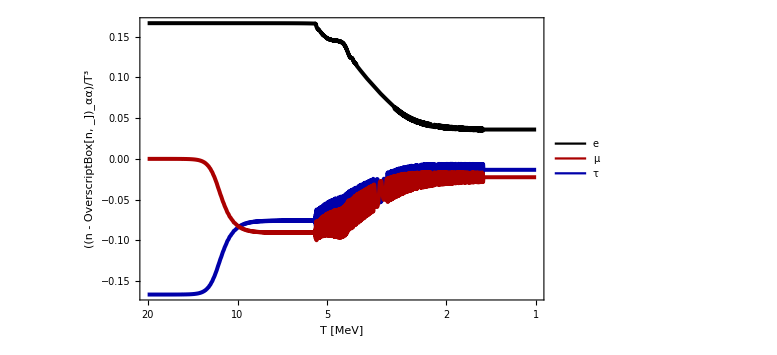

```mathematica
Aval=√2;
ϕval=0;

ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];

Fig6aFD=solveFD[ξeini,ξμini,ξτini]
```

#### Benchmarks of the paper with collision terms in the damping approximation

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: 0.0000765606

Thermodynamics are output to: output/Fig5aD.dat

Total execution time: 1.962 s

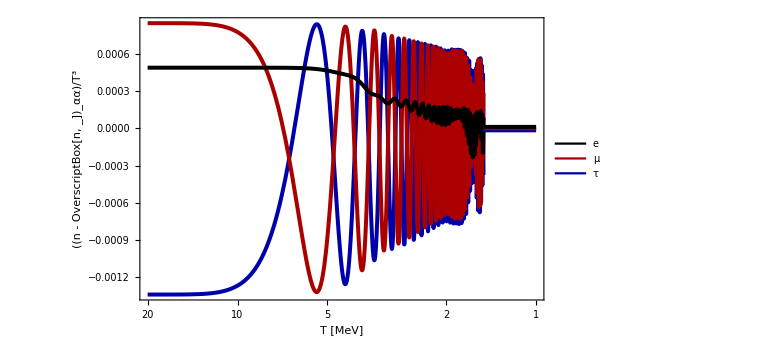

```mathematica
(*Running in the damping approximation is typically much faster*)
Aval=0.01;
ϕval=π/3;

ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];
Tini=20MeV;
Tave=1.5MeV;
Tfinal=1MeV;
accval=10;
precval=10;

(*The function solveDamping receives the same arguments as solveFD*)
Fig5aD=solveDamping[ξeini,ξμini,ξτini,"Fig5aD",Tini,Tave,Tfinal,accval,precval]
```

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: -0.0190749

Thermodynamics are output to: output/Fig5bD.dat

Total execution time: 18.46 s

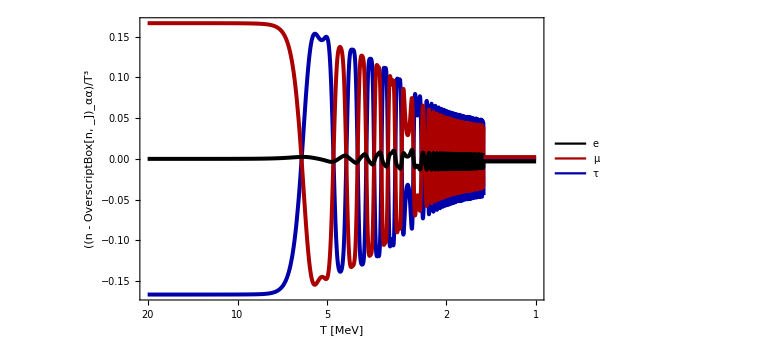

```mathematica
(*Running in the damping approximation is typically much faster*)
Aval=√2;
ϕval=π/2;

ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];
Tini=20MeV;
Tave=1.5MeV;
Tfinal=1MeV;
accval=10;
precval=10;

(*The function solveDamping receives the same arguments as solveFD*)
Fig5bD=solveDamping[ξeini,ξμini,ξτini,"Fig5bD",Tini,Tave,Tfinal,accval,precval]
```

```mathematica
(*The next two benchmarks work better with StiffnessSwitching than with BDF*)
```

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: 0.0120714

Thermodynamics are output to: output/Fig12a.dat

Total execution time: 1.217 min

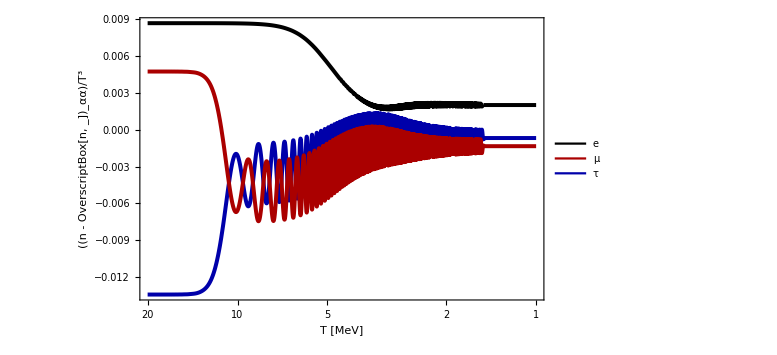

```mathematica
Aval=0.1;
ϕval=0.5;
ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];
Tini=20MeV;
Tave=1.5MeV;
Tfinal=1MeV;
accval=8;
precval=8;

Fig12a=solveDamping[ξeini,ξμini,ξτini,"Fig12a",Tini,Tave,Tfinal,accval,precval,"StiffnessSwitching"]
```

Starting evolution of the full system

System evolved until T_ave=1.5 MeV

Final ξe: 0.122708

Thermodynamics are output to: output/Fig12b.dat

Total execution time: 1.207 min

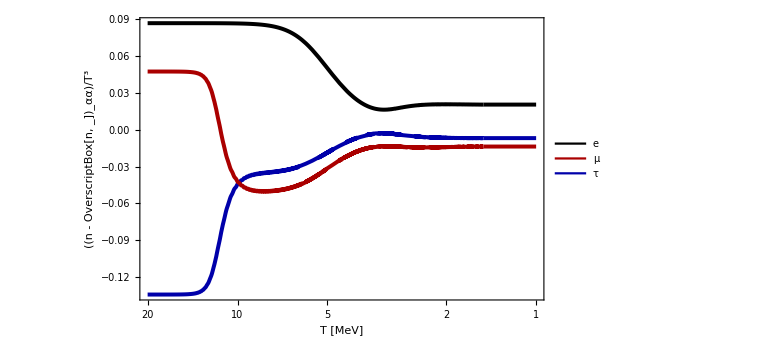

```mathematica
Aval=1;
ϕval=0.5;
ξeini=ξtildetoξ[ξtile[Aval,ϕval]];
ξμini=ξtildetoξ[ξtilμ[Aval,ϕval]];
ξτini=ξtildetoξ[ξtilτ[Aval,ϕval]];
Tini=20MeV;
Tave=1.5MeV;
Tfinal=1MeV;
accval=7;
precval=7;

Fig12b=solveDamping[ξeini,ξμini,ξτini,"Fig12b",Tini,Tave,Tfinal,accval,precval,"StiffnessSwitching"]
```